Predator-Prey Relationships with Edible Habitat Complexity in Benthic Communities

Eden Forbes, 2025

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ClearAll["Global`*"]
Quiet[<<"/Users/eden/Desktop/RESEARCH/CODE/Dynamica/Dynamica.m"]
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

## Building Block Visualizers

```mathematica
T2[x_]:=(595/(30+ x));
```

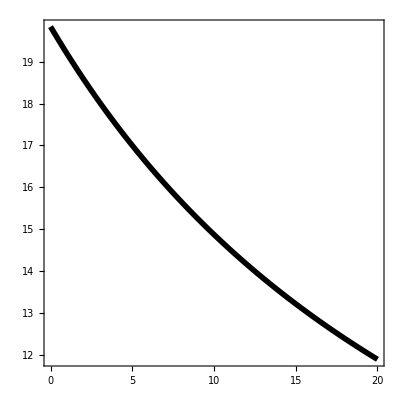

```mathematica
Plot[T2[x],{x,0,20},PlotStyle->{Black,Thickness[0.01]},PlotRange->{All,All},Frame->True,LabelStyle->{Black,20},AspectRatio->1
]
```

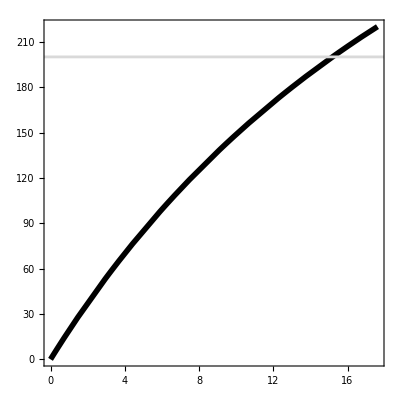

```mathematica
Plot[T2[x]*x,{x,0,300},PlotStyle->{Black,Thickness[0.01]},PlotRange->{All,{0,220}},Frame->True,LabelStyle->{Black,20},AspectRatio->1,GridLines->{{30},{200}}, GridLinesStyle->Thickness[0.005]
]
```

```mathematica
β[rat_,steep_]:= (rat)^steep/((rat)^steep+α^steep); (* When the ratio is 10:1 (1),  start eating Dreissena *)
```

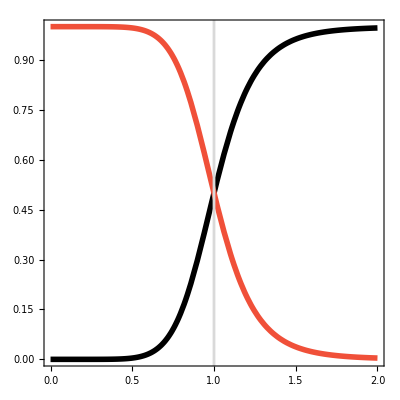

```mathematica
Show[
Plot[β[x,8]/.{α->1},{x,0,2},PlotStyle->{Black,Thickness[0.01]},PlotRange->All],
(*Plot[β[x,1]/.{α->1},{x,0,2},PlotStyle->{Black,Dashed,Thickness[0.01]},PlotRange->All],*)
Plot[1-β[x,8]/.{α->1},{x,0,2},PlotStyle->{RGBColor["#F05039"],Thickness[0.01]},PlotRange->All],
(*Plot[1-β[x,1]/.{α->1},{x,0,2},PlotStyle->{Blue,Dashed,Thickness[0.01]},PlotRange->All],*)
Frame->True,LabelStyle->{Black,20},AspectRatio->1,AxesOrigin->{0,0},GridLines->{{1},{}}, GridLinesStyle->Thickness[0.005]
]
```

## Predator-Prey Subsystem

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,dj,dm,dp,dv,α,ω,r,yj,fjp,δ]
```

```mathematica
PP = DynamicalSystem[{
r*V*(1 - V/kv)-(fvp/(hvp+ V))*V*P - dv V,
((yv ep)/yp)*(fvp/(hvp+ V))*V*P - dp*P
},
{{V,-0.0001,1000},{P,-0.0001,100}},
{{r,0,100},{dv,0.001,0.14},{yv,0.001,0.1},
{ep,0,1},{hvp,0,1},{fvp,0,1},{dp,0.0001,0.01},{yp,0,10000},
{kv,1,1000}
}];
PP = PP/.{r->0.1,kv->1000,dv->1/30, yv->0.67,ep->0.09,hvp->30, fvp->0.08*4900/0.67,yp->4900};
```

```mathematica
PPBD = DisplayBifurcationDiagram[PP,dp,MinStepSize->0.1,MaxSteps->200000]
$BifurcationDiagramBPs
```

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,dp}={666.667,0,0.0001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,dp}={666.667,0,0.01}

-Graphics3D-

{BifurcationPoint[Branch,{0,0},{dp→0,dv→1/30,ep→0.09,fvp→585.075,hvp→30,kv→1000,r→0.1,yp→4900,yv→0.67}],BifurcationPoint[Hopf,{318.333333333333,0.0207385700113379},{dp→0.0065799043062201,dv→1/30,ep→0.09,fvp→585.075,hvp→30,kv→1000,r→0.1,yp→4900,yv→0.67}]}

```mathematica
dV = r*V*(1 - V/kv)-(fvp/(hvp+ V))*V*P - dv V;
dP = ((yv ep)/yp)*(fvp/(hvp+ V))*V*P - dp*P;
```

### Jacobian Elements & Feedbacks

```mathematica
J11 = FullSimplify[D[dV,V]];
J12 = FullSimplify[D[dV,P]];
J21 = FullSimplify[D[dP,V]];
J22 = FullSimplify[D[dP,P]];
```

```mathematica
JM = {{J11,J12},{J21,J22}};
JM//MatrixForm
```

(-dv+r-(2 r V)/kv-(fvp hvp P)/(hvp+V)^2 | -(fvp V)/(hvp+V)
(ep fvp hvp P yv)/((hvp+V)^2 yp) | -dp+(ep fvp V yv)/((hvp+V) yp))

#### Feedback Level 1

```mathematica
L1 = J11+J22;
```

#### Feedback Level 2

```mathematica
L2 = (J12*J21-J11*J22);
```

### CHART

```mathematica
solsPP= Solve[{dV==0,dP==0},{V,P}];
```

```mathematica
solsPP
```

{{V→0,P→0},{V→(-dv kv+kv r)/r,P→0},{V→-(dp hvp yp)/(dp yp-ep fvp yv),P→-(ep hvp yv (-dp dv kv yp+dp hvp r yp+dp kv r yp+dv ep fvp kv yv-ep fvp kv r yv))/(kv (dp yp-ep fvp yv)^2)}}

```mathematica
Vp = solsPP[[2,1,2]];
Vo = solsPP[[3,1,2]];
Po = solsPP[[3,2,2]];
P0=(((yv ep)/yp)*(fvp/(hvp+ Vp))*Vp)/dp;
```

```mathematica
Pin = Solve[P0==1.0,dp][[1]][[1]][[2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(ep fvp kv (dv-1. r) yv)/((dv kv-1. hvp r-1. kv r) yp)

```mathematica
r=0.1; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67;  yp=4900;
```

```mathematica
Pin
```

0.00688995

```mathematica
Show[
RegionPlot[0.006889 > x>-1,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->200,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.00658 > x,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{Gray},PlotPoints->500,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

ListPlot[PPBD[[1]][[1]][[2]][[3]][[1]][[All,{1,2}]],Joined->True,PlotStyle->RGBColor["#1F449C"]],
ListPlot[MapThread[List,{PPBD[[1]][[1]][[2]][[3]][[1]][[All,1]],PPBD[[1]][[1]][[2]][[3]][[1]][[All,3]]*5000}],Joined->True,PlotStyle->RGBColor["#F05039"]],

ListPlot[PPBD[[1]][[1]][[4]][[3]][[1]][[All,{1,2}]],Joined->True,PlotStyle->RGBColor["#1F449C"]],

ListPlot[MapThread[List,{PPBD[[1]][[1]][[4]][[3]][[1]][[All,1]],PPBD[[1]][[1]][[4]][[3]][[1]][[All,3]]*5000}],Joined->True,PlotStyle->RGBColor["#F05039"],Frame->True,FrameTicks->{{None,All},{All,None}},FrameTicksStyle->{{None,RGBColor["#F05039"]},{Black,None}},LabelStyle->18],

FrameTicks->{{All,{{0,"0"},{100,"0.02"},{200,"0.04"},{300,"3"},{400,"4"},{500,"5"}}},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},FrameTicksStyle->{{RGBColor["#1F449C"],RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{0,250}}]
```

-Graphics-

```mathematica
IDD = FullSimplify[D[dV/V,V]];
```

```mathematica
IDD
```

(-0.09+585.075 P+(-0.006-0.0001 V) V)/(30.+V)^2

```mathematica
Show[
RegionPlot[0.006889 > x>-1,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->200,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.00658 > x,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{Gray},PlotPoints->200,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[IDD/.{V->Vo,P->Po},{dp,0.0001,0.006889}, PlotStyle->RGBColor["#1F449C"]],
FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,
LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-0.0005,0.0022}}]
```

-Graphics-

```mathematica
Show[
RegionPlot[0.006889 > x>-1,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->200,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.00658 > x,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{Gray},PlotPoints->200,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[L1/.{V->Vo,P->Po},{dp,0.0001,0.0069},PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
Plot[L2/.{V->Vo,P->Po},{dp,0.0001,0.0069},PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-0.01,0.04}}]
```

-Graphics-

```mathematica
Show[
RegionPlot[0.006889 > x>-1,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->200,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.00658 > x,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{Gray},PlotPoints->200,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[J11/.{V->Vo,P->Po},{dp,0.0001,0.0069},PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
Plot[J22/.{V->Vo,P->Po},{dp,0.0001,0.0069},PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[L1/.{V->Vo,P->Po},{dp,0.0001,0.0069},PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-0.01,0.04}}]
```

-Graphics-

## Combined (D Growth)

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,dj,dm,dp,dv,α,ω,r,δ]
```

```mathematica
β[V_,Z_]:= (V/Z)^ω/((V/Z)^ω+α^ω);
```

```mathematica
FULL = DynamicalSystem[{
r*(1+δ M/kz)*V*(1 - V/(kv*(1+δ M/kz)))-((fvp β[V,M])/(hvp+ V))*V*P - dv V,
((yv ep)/yp)*((fvp β[V,M])/(hvp+ V))*V*P - dp*P,
b M (1-J/kz)-g J - dj J,
g J (1-M/kz)- dm M
},
{{V,-0.01,10000},{P,-0.01,100}, {J,-0.01,10000},{M,-0.01,10000}},
{{r,0,100},{dv,0.001,0.14},{yv,0.001,0.1},
{ep,0,1},{hvp,0,1},{fvp,0,1},{dp,0.0001,0.008},{yp,0,10000},
{α,0.001,1},{ω,1,4},{δ,0,4},
{b,0.0001,2000},{g,0.0001,1000},{kz,0.001,100},{kv,1,2000},{dj,0.0001,1},{dm,0.0001,1}
}]
FULL = FULL/.{b->1370,g->1/270,dj->1/365,dm->1/1460,r->0.1,kz->200,kv->1000,dv->1/30, yv->0.67,ep->0.09,hvp->30, fvp->0.08*4900/0.67,dp->0.004, yp->4900,α->1,ω->4,δ->2};
```

DynamicalSystem[«4 ODEs»,{V,P,J,M},{r,dv,yv,ep,hvp,fvp,dp,yp,α,ω,δ,b,g,kz,kv,dj,dm}]

```mathematica
DisplayBifurcationDiagram[FULL,dp,StateVariables->{V,P}, MaxSteps->Infinity, MinStepSize->0.1]
$BifurcationDiagramBPs
```

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,dp}={0,0,199.999,168.786,0.0001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,dp}={2354.53,0,199.999,168.786,0.0001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,dp}={2354.53,0,199.999,168.786,0.008}

-Graphics3D-

{BifurcationPoint[Branch,{0,0,199.998885403359,168.785980361501},{b→1370,dj→1/365,dm→1/1460,dp→0,dv→1/30,ep→0.09,fvp→585.075,g→1/270,hvp→30,kv→1000,kz→200,r→0.1,yp→4900,yv→0.67,α→1,δ→2,ω→4}],BifurcationPoint[Hopf,{241.044445473069,0.121448995015539,199.998885403359,168.785980361501},{b→1370,dj→1/365,dm→1/1460,dp→0.00516205934981656,dv→1/30,ep→0.09,fvp→585.075,g→1/270,hvp→30,kv→1000,kz→200,r→0.1,yp→4900,yv→0.67,α→1,δ→2,ω→4}],BifurcationPoint[Hopf,{1161.17067518634,0.243067289257838,199.998885403359,168.785980361501},{b→1370,dj→1/365,dm→1/1460,dp→0.00701553378289946,dv→1/30,ep→0.09,fvp→585.075,g→1/270,hvp→30,kv→1000,kz→200,r→0.1,yp→4900,yv→0.67,α→1,δ→2,ω→4}]}

#### Funcs

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1;kz = 200; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67;  yp=4900; α=1; ω=4; δ=2; dp = 0.004;
```

```mathematica
TS=NDSolveValue[
{ V'[t]==r*V[t]*(1 - V[t]/kv)-(fvp/(hvp+ V[t]))*V[t]*P[t] - dv V[t],
P'[t]==((yv ep)/yp)*(fvp/(hvp+ V[t]))*V[t]*P[t] - dp*P[t],
Pplot'[t] == 100*P[t] - Pplot[t],

V[0]==1000,P[0]==1, Pplot[0]==0
},{V,Pplot},{t,0,10000}];
(*TS2=NDSolveValue[
{ V'[t]==r*(1+δ M[t]/kz)*V[t]*(1 - V[t]/(kv*(1+δ M[t]/kz)))-((fvp β[V[t],M[t]])/(hvp+ V[t]))*V[t]*P[t] - dv V[t],
P'[t]==((yv ep)/yp)*((fvp β[V[t],M[t]])/(hvp+ V[t]))*V[t]*P[t] - dp*P[t],
J'[t]==b M[t](1-J[t]/kz) -g J[t] - dj J[t],
M'[t]==g J[t](1-M[t]/kz)- dm M[t],

V[0]==680,P[0]==0.5,J[0]==50, M[0]==50, 
WhenEvent[t==5500,{V[t]->680,P[t]->0.000008,J[t]->1,M[t]->1}]
},{V,P,J,M},{t,0,10000}];*)
```

NDSolveValue::ndsz: At t == 2069.94, step size is effectively zero; singularity or stiff system suspected.

#### Plots

InterpolatingFunction::dmval: Input value {2500.} lies outside the range of data in the interpolating function. Extrapolation will be used.

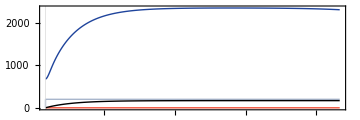

```mathematica
Show[
Plot[Evaluate[#[t]& /@TS],{t,2500,5500},PlotRange->All,ImageSize->Medium,
 PlotStyle->{{RGBColor["#1F449C"],Thick},{RGBColor["#F05039"],Thick},{RGBColor["#A8B6CC"],Thick},{Black,Thick}},
PlotPoints->1000],
Plot[Evaluate[#[t]& /@TS2],{t,5500,8000},PlotRange->All,ImageSize->Medium,
 PlotStyle->{{RGBColor["#1F449C"],Thick},{RGBColor["#F05039"],Thick},{RGBColor["#A8B6CC"],Thick},{Black,Thick}},
PlotPoints->1000],
TicksStyle->10,AxesOrigin->{2500,-20},
AspectRatio->1/3, LabelStyle->16, Frame->True,  FrameStyle->Black,
GridLines->{{5500},{}},GridLinesStyle->{Dashed,Thick}
]
```

## PCHART

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,dj,dm,dp,dv,α,ω,r,δ]
```

```mathematica
dV = r*(1+δ M/kz)*V*(1 - V/(kv(1+δ M/kz)))-((fvp β[V,M])/(hvp+ V))*V*P - dv V;
dP = ((yv ep)/yp)*((fvp β[V,M])/(hvp+ V))*V*P - dp*P ;
dJ = b M (1-J/kz)-g J - dj J;
dM = g J (1-M/kz)- dm M;
```

### Jacobian Elements & Feedbacks

```mathematica
J11 = FullSimplify[D[dV,V]];
J12 = FullSimplify[D[dV,P]];
J13 = FullSimplify[D[dV,J]];
J14 = FullSimplify[D[dV,M]];
```

```mathematica
J21 = FullSimplify[D[dP,V]];
J22 = FullSimplify[D[dP,P]];
J23 = FullSimplify[D[dP,J]];
J24 = FullSimplify[D[dP,M]];
```

```mathematica
J31 = FullSimplify[D[dJ,V]];
J32 = FullSimplify[D[dJ,P]];
J33 = FullSimplify[D[dJ,J]];
J34 = FullSimplify[D[dJ,M]];
```

```mathematica
J41 = FullSimplify[D[dM,V]];
J42 = FullSimplify[D[dM,P]];
J43 = FullSimplify[D[dM,J]];
J44 = FullSimplify[D[dM,M]];
```

```mathematica
JM = {{J11,J12,J13,J14},{J21,J22,J23,J24},{J31,J32,J33,J34},{J41,J42,J43,J44}};
JM//MatrixForm
```

(-dv+r (1-(2 V)/kv+(M δ)/kz)-(fvp P (V/M)^ω (hvp (V/M)^ω+α^ω (hvp+(hvp+V) ω)))/((hvp+V)^2 ((V/M)^ω+α^ω)^2) | -(fvp V (V/M)^ω)/((hvp+V) ((V/M)^ω+α^ω)) | 0 | (V (hvp M r ((V/M)^ω+α^ω)^2 δ+M r V ((V/M)^ω+α^ω)^2 δ+fvp kz P (V/M)^ω α^ω ω))/(kz M (hvp+V) ((V/M)^ω+α^ω)^2)
(ep fvp P (V/M)^ω yv (hvp (V/M)^ω+α^ω (hvp+(hvp+V) ω)))/((hvp+V)^2 yp ((V/M)^ω+α^ω)^2) | -dp+(ep fvp V (V/M)^ω yv)/((hvp+V) yp ((V/M)^ω+α^ω)) | 0 | -(ep fvp P V yv ω Sech[1/2 ω (Log[V/M]-Log[α])]^2)/(4 hvp M yp+4 M V yp)
0 | 0 | -((dj+g) kz+b M)/kz | b-(b J)/kz
0 | 0 | g-(g M)/kz | -(g J+dm kz)/kz)

```mathematica
(* Make a dummy Jacobian *)
DJac = {{jVV,jVP,0,jVM},{jPV,jPP,0,jPM},{0,0,jJJ,jJM},{0,0,jMJ,jMM}};
DJac//MatrixForm
```

(jVV | jVP | 0 | jVM
jPV | jPP | 0 | jPM
0 | 0 | jJJ | jJM
0 | 0 | jMJ | jMM)

```mathematica
Expand[CharacteristicPolynomial[DJac,x]]
```

jJM jMJ jPV jVP-jJJ jMM jPV jVP-jJM jMJ jPP jVV+jJJ jMM jPP jVV+jJM jMJ jPP x-jJJ jMM jPP x+jJJ jPV jVP x+jMM jPV jVP x+jJM jMJ jVV x-jJJ jMM jVV x-jJJ jPP jVV x-jMM jPP jVV x-jJM jMJ x^2+jJJ jMM x^2+jJJ jPP x^2+jMM jPP x^2-jPV jVP x^2+jJJ jVV x^2+jMM jVV x^2+jPP jVV x^2-jJJ x^3-jMM x^3-jPP x^3-jVV x^3+x^4

#### Feedback Level 1

```mathematica
Tr[DJac]
```

jJJ+jMM+jPP+jVV

```mathematica
L1 = J11+J22+J33+J44;
```

#### Feedback Level 2

```mathematica
L2 = (J12*J21-J11*J22)+(J43*J34-J33*J44)+(-J11*J44)+(-J11*J33)+(-J22*J44)+(-J22*J33);
```

#### Feedback Level 3

```mathematica
L3 = -(J34 J43 J22 -J33 J44 J22 + J33 J21 J12 + J44 J21 J12 + J34 J43 J11 - J33 J44 J11 - J33 J22 J11 - J44 J22 J11);
```

#### Feedback Level 4

```mathematica
Det[DJac]
```

jJM jMJ jPV jVP-jJJ jMM jPV jVP-jJM jMJ jPP jVV+jJJ jMM jPP jVV

```mathematica
L4 =-(J34 J43 J12 J21-J33 J44 J12 J21-J34 J43 J22 J11+J11 J22 J33 J44);
```

#### Oscillation Criterion

```mathematica
OC = ((L1*L2+L3)*L3)/L1^2-L4;
```

### CHART - dp

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1;kz = 200; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67;  yp=4900; α=1; ω=4; δ=2;
```

```mathematica
solsPP= Solve[{dV==0,dP==0, dJ==0, dM==0},{V,P,J,M}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
solsPP[[7]]/.dp->0.004
```

{V→195.105,P→0.129618,J→199.999,M→168.786}

```mathematica
Vp = Re[solsPP[[3,1,2]]];
Jp = Re[solsPP[[3,3,2]]];
Mp = Re[solsPP[[3,4,2]]];

Vo = Re[solsPP[[7,1,2]]];
Po = Re[solsPP[[7,2,2]]];
Jo = Re[solsPP[[7,3,2]]];
Mo = Re[solsPP[[7,4,2]]];

P0=(((yv ep)/yp)*((fvp β[Vp,Mp])/(hvp+ Vp))*Vp)/dp;
```

```mathematica
FindRoot[P0==1,{dp,0.065}]
```

{dp→0.00710923}

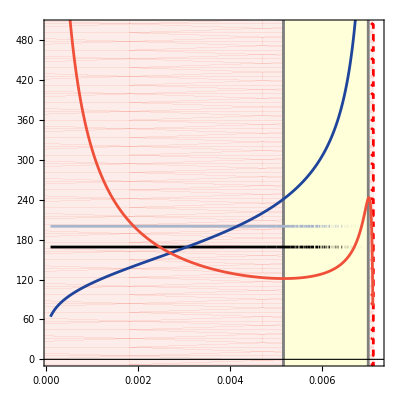

```mathematica
Show[
RegionPlot[0.00711> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.00516,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[Jo,{dp,0.0001,0.0071},PlotStyle->RGBColor["#A8B6CC"], PlotPoints->400],
Plot[Mo,{dp,0.0001,0.0071},PlotStyle->Black, PlotPoints->400],
Plot[Vo,{dp,0.0001,0.0071},PlotStyle->RGBColor["#1F449C"], PlotPoints->400],
Plot[Po*1000,{dp,0.00,0.0071},PlotStyle->RGBColor["#F05039"], PlotPoints->400,PlotRange->All],

Frame->True,FrameTicks->{{All,{{0,"0.0"},{100,"0.1"},{200,"0.2"},{300,"0.3"},{400,"0.4"},{500,"0.5"}}},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{0,500}}]
```

```mathematica
IDD = FullSimplify[D[dV/V,V]]
```

(M^8 (-0.09+(-0.006-0.0001 V) V)+V^8 (-0.09+585.075 P+(-0.006-0.0001 V) V)+M^4 V^3 (P (-70209.-1755.22 V)+V (-0.18+(-0.012-0.0002 V) V)))/((30.+V)^2 (M^4+V^4)^2)

```mathematica
FullSimplify[D[(V/Z)^ω/((V/Z)^ω+α^ω),V]]
```

(4 V^3 Z^4)/((V^4+Z^4)^2)

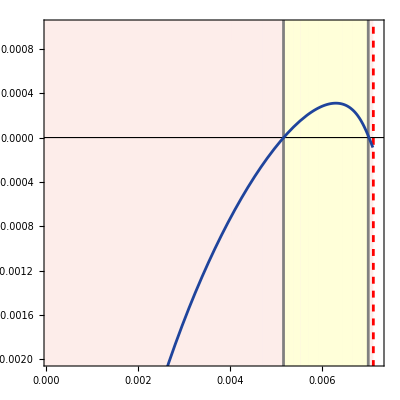

```mathematica
Show[
RegionPlot[0.00711> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.00516,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[IDD/.{V->Vo,P->Po, J->Jo, M->Mo},{dp,0.0001,0.0071 }, PlotStyle->RGBColor["#1F449C"]],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
Frame->True,
LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-0.002,0.001}}]
```

#### Loops kz = 200

```mathematica
Quiet[FindRoot[(OC/.{V->Vo,P->Po,J->Jo,M->Mo})==0,{dp,0.03}]]
Quiet[FindRoot[(OC/.{V->Vo,P->Po,J->Jo,M->Mo})==0,{dp,0.0638}]]
```

{dp→0.045885}

{dp→0.0623603}

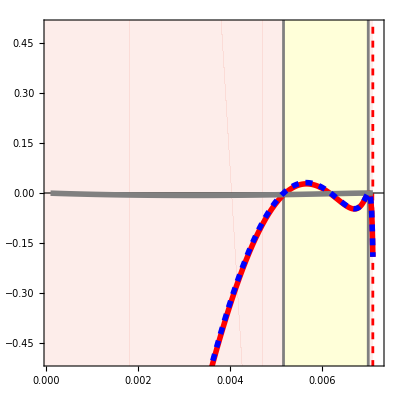

```mathematica
Show[
RegionPlot[0.0071> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.00516,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[((L1*L2+L3)*L3)/L1^2/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
Plot[L4/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[OC/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-0.5,0.5}}]
```

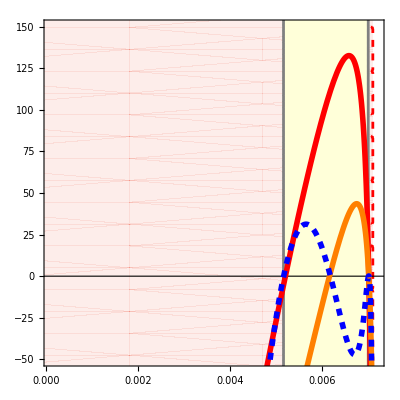

```mathematica
Show[
RegionPlot[0.0071> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.00516,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],
Plot[L2/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
Plot[L3*100/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Orange,Thickness->0.01},PlotPoints->100],
Plot[OC*1000/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-50,150}}]
```

```mathematica
Show[
RegionPlot[0.0071> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},
PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.005162,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->1000,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],
Plot[L2/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
Plot[OC*1000/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0051,0.0053},{-5,5}}]
```

-Graphics-

```mathematica
Show[
RegionPlot[0.0071> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.00516,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

(*Plot[(J12*J21-J11*J22)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0639},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[(J13*J31-J11*J33)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0639},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[(-J11*J44)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0639},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],*)
Plot[(-J11*J33)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
(*Plot[(-J22*J44)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0639},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[(-J22*J33)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0639},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
*)
Plot[L2/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-50,150}}]
```

-Graphics-

```mathematica
Show[
RegionPlot[0.0071> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.00516,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[(J11)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Red,Thickness->0.01},PlotPoints->100],

Plot[-J11*J33*0.001/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100,PlotRange->All],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-0.1,0.15}}]
```

-Graphics-

```mathematica
Show[
RegionPlot[0.0071> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.00516,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

(*Plot[(J33 J22 J11)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.00779},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10],
Plot[(J44 J22 J11)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.00779},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10],*)
Plot[(J33 J44 J11)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Orange,Thickness->0.01},PlotPoints->10],
Plot[(-J34 J43 J11)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10],
Plot[(-J44 J21 J12)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10],
Plot[(-J33 J21 J12 )/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Red,Thickness->0.01},PlotPoints->10],
Plot[(J33 J44 J22)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Rwed,Thickness->0.01},PlotPoints->10],
Plot[(-J34 J43 J22 )/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10],
Plot[L3/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-2,1}}]
```

-Graphics-

```mathematica
Show[
RegionPlot[0.0071> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.00516,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[(J11)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Orange,Thickness->0.01},PlotPoints->10],
Plot[(J33)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10, PlotRange->All],
Plot[(J44)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10,PlotRange->All],
Plot[J33 J44 J11/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-0.5,0.6}}]
```

-Graphics-

### CHART - kz

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,dj,dm,dp,dv,α,ω,r,δ]
```

```mathematica
DisplayBifurcationDiagram[FULL,kz,StateVariables->{V,P}, MaxSteps->Infinity, MinStepSize->0.1]
$BifurcationDiagramBPs
```

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,kz}={105.937,0.0732854,99.9994,84.393,100}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,kz}={2354.53,0,99.9994,84.393,100}

-Graphics3D-

{}

```mathematica
Clear[kz]
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67;  yp=4900;dp=0.004; α=1; ω=4; δ=2;
```

```mathematica
solsKZ= Solve[{dV==0,dP==0, dJ==0, dM==0},{V,P,J,M}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
solsKZ[[7]]/.kz->100
```

{V→,P→0.0732854,J→99.9994,M→84.393}

```mathematica
Vp = Re[solsKZ[[4,1,2]]];
Jp = Re[solsKZ[[4,3,2]]];
Mp = Re[solsKZ[[4,4,2]]];

Vo = Re[solsKZ[[7,1,2]]];
Po = Re[solsKZ[[7,2,2]]];
Jo = Re[solsKZ[[7,3,2]]];
Mo = Re[solsKZ[[7,4,2]]];

P0=(((yv ep)/yp)*((fvp β[Vp,Mp])/(hvp+ Vp))*Vp)/dp;
```

```mathematica
FindRoot[P0==1,{kz,2800}]
```

{kz→2619.7}

```mathematica
Show[
LogPlot[x=0,{x,-1,3100},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[x>78,{x,-100,2619.7},{y,-100,3000}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[78>x>-100,{x,-100,2000},{y,-100,3000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->{LightYellow}],
LogPlot[x=0,{x,-1,3100},PlotStyle->{Black,Thickness[0.002]}],

LogPlot[Vo,{kz,1,3000},PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}, PlotPoints->500,PlotRange->All],
LogPlot[Jo,{kz,1,3000},PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}, PlotPoints->500,PlotRange->All],
LogPlot[Mo,{kz,1,3000},PlotStyle->{Black,Thickness[0.01]}, PlotPoints->500,PlotRange->All],
LogPlot[Po*1000,{kz,1,3000},PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}, PlotPoints->500,PlotRange->All],


Frame->True,FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{1,2800},{3,8}}]
```

-Graphics-

### CHART - alpha

```mathematica
Quiet[DisplayBifurcationDiagram[FULL,α,MaxSteps->100000]]
$BifurcationDiagramBPs
```

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,α}={37.5,0.0267315,199.999,168.786,0.001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,α}={2354.53,0,199.999,168.786,0.001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,α}={2354.53,0,199.999,168.786,1}

-Graphics-

{BifurcationPoint[Hopf,{58.3365666775923,0.0412106922223758,199.998885403359,168.785980361501},{b→1370,dj→1/365,dm→1/1460,dp→0.004,dv→1/30,ep→0.09,fvp→585.075,g→1/270,hvp→30,kv→1000,kz→200,r→0.1,yp→4900,yv→0.67,α→0.227797211207245,δ→2,ω→4}]}

#### Sims

```mathematica
Clear[α];
```

```mathematica
min = 0.005; max =0.5; gran = 0.005;
Vpeaks = List[];
Vmeans = List[];
Vvalleys = List[];
Pvalleys = List[];
Ppeaks = List[];
Pmeans = List[];
Jvalleys = List[];
Jpeaks = List[];
Jmeans = List[];
Mpeaks = List[];
Mmeans = List[];
Mvalleys = List[];
```

```mathematica
Clear[i,j,l];
For[i=(min/gran),i<=(max/gran),i++,
(* Transient *)
DisplayTrajectories[FULL/.{kz->200,α->i*gran},{{58.64,0.036,49.99,42.196}},200000,MaxSteps->500000,PlotRange->All];
(* Simulation *)
DisplayTrajectories[FULL/.{kz->200,α->i*gran},{Last[First[$Trajectories]]},20000, MaxSteps->Infinity, PlotPoints->1000];

(* Data Collection *)
vpeaks = Max[$Trajectories[[1]][[All,1]]];
vvalleys = Min[$Trajectories[[1]][[All,1]]];
ppeaks = Max[$Trajectories[[1]][[All,2]]];
pvalleys = Min[$Trajectories[[1]][[All,2]]];

AppendTo[Vpeaks,{i*gran,vpeaks}];
AppendTo[Vvalleys,{i*gran,vvalleys}];
AppendTo[Ppeaks,{i*gran,ppeaks}];
AppendTo[Pvalleys,{i*gran,pvalleys}];

vmean = Mean[$Trajectories[[1]][[All,1]]];
AppendTo[Vmeans,{i*gran,vmean}];
pmean = Mean[$Trajectories[[1]][[All,2]]];
AppendTo[Pmeans,{i*gran,pmean}];
jmean = Mean[$Trajectories[[1]][[All,3]]];
AppendTo[Jmeans,{i*gran,jmean}];
mmean = Mean[$Trajectories[[1]][[All,4]]];
AppendTo[Mmeans,{i*gran,mmean}];
]
```

```mathematica
Show[
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[5>x>0.2277,{x,-5,5},{y,-100,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.2277 > x>0,{x,-1,1},{y,-100,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],

ListLogPlot[Jmeans,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}],
ListLogPlot[Mmeans,Joined->True, PlotStyle->{Black,Thickness[0.01]}],

ListLogPlot[Vvalleys,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed}],
ListLogPlot[Vmeans,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],
ListLogPlot[Vpeaks, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],

ListLogPlot[MapThread[List,{Pvalleys[[All,1]],Pvalleys[[All,2]]*1000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListLogPlot[MapThread[List,{Pmeans[[All,1]],Pmeans[[All,2]]*1000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],
ListLogPlot[MapThread[List,{Ppeaks[[All,1]],Ppeaks[[All,2]]*1000}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],


Frame->True,(*FrameTicks->{{All,{{1,"10^-3"},{5,"5*10^-3"},{10,"10^-2"},{50,"5*10^-2"},{100,"10^-1"},{500,"5*10^-1"},{1000,"1"}}},{All,None}},*)FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{0,0.5},{0,8}}]
```

-Graphics-

#### Loops

```mathematica
Clear[α]
```

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1;dp=0.004; kz = 200; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67;  yp=4900;  ω=4; δ=2;
```

```mathematica
solsFULL= Solve[{dV==0,dP==0, dJ==0, dM==0},{V,P,J,M}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
solsFULL[[5]]/.α->0.2
```

{V→53.7684,P→0.0380592,J→199.999,M→168.786}

```mathematica
Show[
RegionPlot[5>x>0.2278,{x,-5,5},{y,-100,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.2278 > x>0,{x,-1,1},{y,-100,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

Plot[Re[L1/.solsFULL[[5]]]*0.01,{α,0,0.37}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[L2/.solsFULL[[5]]],{α,0,0.34}, PlotStyle->{Red,Thickness[0.01]}],
Plot[Re[L3/.solsFULL[[5]]],{α,0,0.37}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[L4/.solsFULL[[5]]],{α,0,0.37}, PlotStyle->{Gray,Thickness[0.01]}],

Plot[Re[L1/.solsFULL[[7]]]*0.01,{α,0.37,0.6}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[L3/.solsFULL[[7]]],{α,0.37,0.6}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[L4/.solsFULL[[7]]],{α,0.37,0.6}, PlotStyle->{Gray,Thickness[0.01]}],

Plot[(OC/.solsFULL[[5]])*1000,{α,0,0.37}, PlotStyle->{Blue,Dashed,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[(OC/.solsFULL[[7]])*1000,{α,0.37,0.6}, PlotStyle->{Blue,Dashed,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{{0,0.5},{-50,50}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>0.2278,{x,-5,5},{y,-200,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.2278 > x>0,{x,-1,1},{y,-200,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

Plot[Re[(-J11*J33)/.solsFULL[[5]]],{α,0,0.37}, PlotStyle->{Red,Thickness[0.01]}],
Plot[Re[(-J11*J33)/.solsFULL[[7]]],{α,0.374,0.5}, PlotStyle->{Red,Thickness[0.01]}],

Plot[Re[L2/.solsFULL[[5]]],{α,0,0.37}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],
Plot[Re[L2/.solsFULL[[7]]],{α,0.374,0.5}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],
(*Plot[Re[(J12*J21-J11*J22)/.solsFULL[[11]]],{α,0,1}, PlotStyle->{Red,Thickness[0.01]}],
Plot[Re[(J13*J31-J11*J33)/.solsFULL[[11]]],{α,0,1}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(-J11*J44)/.solsFULL[[11]]],{α,0,1}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(-J11*J33)/.solsFULL[[11]]],{α,0,1}, PlotStyle->{Red,Thickness[0.01]}],
Plot[Re[(-J22*J44)/.solsFULL[[11]]],{α,0,1}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(-J22*J33)/.solsFULL[[11]]],{α,0,1}, PlotStyle->{Gray,Thickness[0.01]}],

Plot[(L2/.solsFULL[[11]]),{α,0,1}, PlotStyle->{Blue,Dashed,Thickness[0.01]},AspectRatio->1,LabelStyle->16],*)

PlotRange->{{0,0.5},{-120,100}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>0.2278,{x,-5,5},{y,-200,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.2278 > x>0,{x,-1,1},{y,-200,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

Plot[Re[(J11)*100/.solsFULL[[5]]],{α,0,0.37}, PlotStyle->{Red,Thickness[0.01]}],
Plot[Re[(J11*100)/.solsFULL[[7]]],{α,0.374,0.5}, PlotStyle->{Red,Thickness[0.01]}],

(*Plot[Re[(J33)*0.001/.solsFULL[[5]]],{α,0,0.36}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(J33)*0.001/.solsFULL[[7]]],{α,0.365,1}, PlotStyle->{Gray,Thickness[0.01]}],*)

Plot[Re[(-J11*J33)/.solsFULL[[5]]],{α,0,0.37}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],
Plot[Re[(-J11*J33)/.solsFULL[[7]]],{α,0.374,0.5}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{0,0.5},{-120,100}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True,AspectRatio->1,LabelStyle->16
]
```

-Graphics-

### CHART - omega

```mathematica
OMBD1=Quiet[DisplayBifurcationDiagram[FULL,ω,MaxSteps->100000, StateVariables->{V,P}]]
$BifurcationDiagramBPs
```

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ω}={0,0,199.999,168.786,1}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ω}={2354.53,0,199.999,168.786,1}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ω}={0,0,199.999,168.786,4}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ω}={2354.53,0,199.999,168.786,4}

-Graphics3D-

{BifurcationPoint[Hopf,{218.056083774591,0.143326444105112,199.998885403359,168.785980361501},{b→1370,dj→1/365,dm→1/1460,dp→0.004,dv→1/30,ep→0.09,fvp→585.075,g→1/270,hvp→30,kv→1000,kz→200,r→0.1,yp→4900,yv→0.67,α→1,δ→2,ω→2.11133588133511}]}

```mathematica
OMBD2 = Quiet[DisplayBifurcationDiagram[FULL,ω,MaxSteps->100000, StateVariables->{J,M}]]
```

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ω}={0,0,199.999,168.786,1}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ω}={666.667,0,0,0,1}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ω}={2354.53,0,199.999,168.786,1}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ω}={0,0,199.999,168.786,4}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ω}={2354.53,0,199.999,168.786,4}

-Graphics3D-

#### Sims

```mathematica
DJac
```

{{jVV,jVP,0,jVM},{jPV,jPP,0,jPM},{0,0,jJJ,jJM},{0,0,jMJ,jMM}}

```mathematica
Clear[ω];
```

```mathematica
min = 1; max =4; gran = 0.02;
Vpeaks = List[];
Vmeans = List[];
Vvalleys = List[];
Pvalleys = List[];
Ppeaks = List[];
Pmeans = List[];
Jvalleys = List[];
Jpeaks = List[];
Jmeans = List[];
Mpeaks = List[];
Mmeans = List[];
Mvalleys = List[];
```

```mathematica
Clear[i,j,l];
For[i=(min/gran),i<=(max/gran),i++,
(* Transient *)
DisplayTrajectories[FULL/.{kz->200,ω->i*gran},{{58.64,0.036,49.99,42.196}},100000,PlotRange->All];
(* Simulation *)
DisplayTrajectories[FULL/.{kz->200,ω->i*gran},{Last[First[$Trajectories]]},10000, MaxSteps->Infinity, PlotPoints->500];

(* Data Collection *)
vpeaks = Max[$Trajectories[[1]][[All,1]]];
vvalleys = Min[$Trajectories[[1]][[All,1]]];
ppeaks = Max[$Trajectories[[1]][[All,2]]];
pvalleys = Min[$Trajectories[[1]][[All,2]]];

AppendTo[Vpeaks,{i*gran,vpeaks}];
AppendTo[Vvalleys,{i*gran,vvalleys}];
AppendTo[Ppeaks,{i*gran,ppeaks}];
AppendTo[Pvalleys,{i*gran,pvalleys}];

vmean = Mean[$Trajectories[[1]][[All,1]]];
AppendTo[Vmeans,{i*gran,vmean}];
pmean = Mean[$Trajectories[[1]][[All,2]]];
AppendTo[Pmeans,{i*gran,pmean}];
jmean = Mean[$Trajectories[[1]][[All,3]]];
AppendTo[Jmeans,{i*gran,jmean}];
mmean = Mean[$Trajectories[[1]][[All,4]]];
AppendTo[Mmeans,{i*gran,mmean}];

]
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 12248.8.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 12341.4.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 12035.7.

General::stop: Further output of NDSolve::mxst will be suppressed during this calculation.

```mathematica
Show[
LogPlot[x=0,{x,-1,5},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[5>x>2.111,{x,-5,5},{y,-100,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[2.111 > x>0,{x,-1,3},{y,-100,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
LogPlot[x=0,{x,-1,5},PlotStyle->{Black,Thickness[0.002]}],

ListLogPlot[Jmeans,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}],
ListLogPlot[Mmeans,Joined->True, PlotStyle->{Black,Thickness[0.01]}],

ListLogPlot[Vvalleys,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed}],
ListLogPlot[Vmeans,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],
ListLogPlot[Vpeaks, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],

ListLogPlot[MapThread[List,{Pvalleys[[All,1]],Pvalleys[[All,2]]*1000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListLogPlot[MapThread[List,{Pmeans[[All,1]],Pmeans[[All,2]]*1000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],
ListLogPlot[MapThread[List,{Ppeaks[[All,1]],Ppeaks[[All,2]]*1000}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],


Frame->True,(*FrameTicks->{{All,{{1,"10^-3"},{5,"5*10^-3"},{10,"10^-2"},{50,"5*10^-2"},{100,"10^-1"},{500,"5*10^-1"},{1000,"1"}}},{All,None}},*)FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{1,3},{0,8}}]
```

-Graphics-

#### Loops

```mathematica
Clear[ω];
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1;dp=0.004; kz = 200; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67;  yp=4900; δ=2; α=1;
```

```mathematica
omegs = Join[OMBD1[[1]][[1]][[1]][[3]][[1]][[All,1]],OMBD1[[1]][[1]][[2]][[3]][[1]][[All,1]]];
Vs = Join[OMBD1[[1]][[1]][[1]][[3]][[1]][[All,2]],OMBD1[[1]][[1]][[2]][[3]][[1]][[All,2]]];
Ps = Join[OMBD1[[1]][[1]][[1]][[3]][[1]][[All,3]],OMBD1[[1]][[1]][[2]][[3]][[1]][[All,3]]];
Js = Join[OMBD2[[1]][[1]][[1]][[3]][[1]][[All,2]],OMBD2[[1]][[1]][[2]][[3]][[1]][[All,2]]];
Ms = Join[OMBD2[[1]][[1]][[1]][[3]][[1]][[All,3]],OMBD2[[1]][[1]][[2]][[3]][[1]][[All,3]]];
```

```mathematica
Show[
RegionPlot[5>x>2.111,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[2.111 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLinePlot[
Transpose[{omegs,Re[((L1*L2+L3)*L3)/L1^2/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Red,Thickness[0.01]}, PlotRange->All],
ListLinePlot[
Transpose[{omegs,Re[-L4/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}, PlotRange->All],

ListLinePlot[
Transpose[{omegs,Re[OC/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Blue,Dashed,Thickness[0.01]}, PlotRange->All],

PlotRange->{{1,3},{-0.15,0.05}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>2.111,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[2.111 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLinePlot[
Transpose[{omegs,Re[L1/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}, PlotRange->All],
ListLinePlot[
Transpose[{omegs,Re[L3/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}, PlotRange->All],
ListLinePlot[
Transpose[{omegs,Re[L4/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}, PlotRange->All],
ListLinePlot[
Transpose[{omegs,Re[L2/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]*0.1}], PlotStyle->{Red,Thickness[0.01]}, PlotRange->All],

ListLinePlot[
Transpose[{omegs,Re[OC/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]*100}], PlotStyle->{Blue,Dashed,Thickness[0.01]}, PlotRange->All],

PlotRange->{{1,3},{-2,3}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>2.111,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[2.111 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLinePlot[
Transpose[{omegs,Re[-J11 J33/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Red,Thickness[0.01]}],

ListLinePlot[
Transpose[{omegs,Re[L2/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{1,3},{-100,100}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>2.111,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[2.111 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLinePlot[
Transpose[{omegs,Re[-J11/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Red,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[J33/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],

ListLinePlot[
Transpose[{omegs,Re[-J11 J33/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]*0.001}], PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{1,3},{-0.1,0.1}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

## Edible Dreissena (D Growth)

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,dj,dm,dp,dv,α,ω,r,yj,fjp,δ]
```

```mathematica
β[V_,Z_]:= (V/Z)^ω/((V/Z)^ω+α^ω);
```

```mathematica
EDIB = DynamicalSystem[{
r*(1+δ M/kz)*V*(1 - V/(kv(1+δ M/kz)))-((fvp β[V,M])/(hvp+β[V,M] V + (1-β[V,M]) J))*V*P - dv V,
(((((yv ep)/yp)fvp β[V,M]V)+(((yj ep)/yp)(1-β[V,M])fjp J))/(hvp+β[V,M] V + (1-β[V,M]) J))*P - dp*P ,
b M (1-J/kz)-g J -(((1-β[V,M]) fjp)/(hvp+β[V,M] V + (1-β[V,M]) J)) *J*P- dj J,
g J (1-M/kz)- dm M
},
{{V,-0.01,100000},{P,-0.01,100000}, {J,-0.01,10000},{M,-0.01,10000}},
{{r,0,1},{dv,0.001,0.14},{yv,0.001,0.1},
{ep,0,1},{hvp,0,1},{fvp,0,1},{fjp,0,1},{dp,0.0001,0.008},{yp,0,10000},{yj,0,10000},
{α,0.0001,1},{ω,1,4},{δ,1,3},
{b,0.0001,2000},{g,0.0001,1000},{kz,1,1000},{kv,100,100000000},{dj,0.0001,1},{dm,0.0001,1}
}]
EDIB = EDIB/.{b->1370,g->1/270,dj->1/365,dm->1/1460,r->0.1,kz->200,kv->1000,dv->1/30, yv->0.67,ep->0.09,hvp-> 30, fvp->0.08*4900/0.67,fjp->0.08*4900/1,dp->0.004,yj->1, yp->4900,α->1,ω->4,δ->2};
```

DynamicalSystem[«4 ODEs»,{V,P,J,M},{r,dv,yv,ep,hvp,fvp,fjp,dp,yp,yj,α,ω,δ,b,g,kz,kv,dj,dm}]

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67; dp=0.004; yp=4900;yj = 1; fjp = 0.08*4900; α=1; ω=4; δ=2;
```

## PCHART

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,yj,fjp,dj,dm,dp,dv,α,ω,r,δ]
```

```mathematica
dV = r*(1+δ M/kz)*V*(1 - V/(kv(1+δ M/kz)))-((fvp β[V,M])/(hvp+β[V,M] V + (1-β[V,M]) J))*V*P - dv V;
dP = (((((yv ep)/yp)fvp β[V,M]V)+(((yj ep)/yp)(1-β[V,M])fjp J))/(hvp+β[V,M] V + (1-β[V,M]) J))*P - dp*P ;
dJ =b M (1-J/kz)-g J -(((1-β[V,M]) fjp)/(hvp+β[V,M] V + (1-β[V,M]) J)) *J*P- dj J;
dM = g J (1-M/kz)- dm M;
```

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67; dp=0.004; yp=4900;yj = 1; fjp = 0.08*4900; α=1; ω=4; δ=2;
```

### Jacobian Elements & Feedbacks

```mathematica
J11 = FullSimplify[D[dV,V]];
J12 = FullSimplify[D[dV,P]];
J13 = FullSimplify[D[dV,J]];
J14 = FullSimplify[D[dV,M]];
```

```mathematica
J21 = FullSimplify[D[dP,V]];
J22 = FullSimplify[D[dP,P]];
J23 = FullSimplify[D[dP,J]];
J24 = FullSimplify[D[dP,M]];
```

```mathematica
J31 = FullSimplify[D[dJ,V]];
J32 = FullSimplify[D[dJ,P]];
J33 = FullSimplify[D[dJ,J]];
J34 = FullSimplify[D[dJ,M]];
```

```mathematica
J41 = FullSimplify[D[dM,V]];
J42 = FullSimplify[D[dM,P]];
J43 = FullSimplify[D[dM,J]];
J44 = FullSimplify[D[dM,M]];
```

```mathematica
JM = {{J11,J12,J13,J14},{J21,J22,J23,J24},{J31,J32,J33,J34},{J41,J42,J43,J44}};
JM//MatrixForm
```

(-dv+r (1-(2 V)/kv+(M δ)/kz)+(fvp P (V/M)^ω (-hvp (V/M)^ω-(hvp+J) α^ω (1+ω)))/(((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2) | -(fvp V (V/M)^ω)/((V/M)^ω (hvp+V)+(hvp+J) α^ω) | (fvp P V (V/M)^ω α^ω)/(((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2) | (V (M r (V/M)^(2 ω) (hvp+V)^2 δ+(hvp+J)^2 M r α^(2 ω) δ+(hvp+J) (V/M)^ω α^ω (2 M r (hvp+V) δ+fvp kz P ω)))/(kz M ((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2)
(ep P (V/M)^ω (-fjp J yj α^ω (V+(hvp+V) ω)+fvp V yv (hvp (V/M)^ω+(hvp+J) α^ω (1+ω))))/(V yp ((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2) | -dp+(ep (fvp V (V/M)^ω yv+fjp J yj α^ω))/((V/M)^ω (hvp+V) yp+(hvp+J) yp α^ω) | (ep P α^ω ((V/M)^ω (fjp (hvp+V) yj-fvp V yv)+fjp hvp yj α^ω))/(yp ((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2) | (ep P (V/M)^ω (fjp J (hvp+V) yj-fvp (hvp+J) V yv) α^ω ω)/(M yp ((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2)
(fjp J P (V/M)^ω α^ω (V+(hvp+V) ω))/(V ((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2) | -(fjp J α^ω)/((V/M)^ω (hvp+V)+(hvp+J) α^ω) | -dj-g-(b M)/kz-(fjp P α^ω ((V/M)^ω (hvp+V)+hvp α^ω))/(((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2) | b-(b J)/kz-(fjp J P (V/M)^ω (hvp+V) α^ω ω)/(M ((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2)
0 | 0 | g-(g M)/kz | -(g J+dm kz)/kz)

```mathematica
(* Make a dummy Jacobian *)
DJac = {{jVV,jVP,jVJ,jVM},{jPV,jPP,jPJ,jPM},{jJV,jJP,jJJ,jJM},{0,0,jMJ,jMM}};
DJac//MatrixForm
```

(jVV | jVP | jVJ | jVM
jPV | jPP | jPJ | jPM
jJV | jJP | jJJ | jJM
0 | 0 | jMJ | jMM)

```mathematica
Expand[CharacteristicPolynomial[DJac,x]]
```

-jJV jMM jPP jVJ+jJP jMM jPV jVJ+jJV jMJ jPP jVM-jJP jMJ jPV jVM+jJV jMM jPJ jVP-jJV jMJ jPM jVP+jJM jMJ jPV jVP-jJJ jMM jPV jVP-jJP jMM jPJ jVV+jJP jMJ jPM jVV-jJM jMJ jPP jVV+jJJ jMM jPP jVV+jJP jMM jPJ x-jJP jMJ jPM x+jJM jMJ jPP x-jJJ jMM jPP x+jJV jMM jVJ x+jJV jPP jVJ x-jJP jPV jVJ x-jJV jMJ jVM x-jJV jPJ jVP x+jJJ jPV jVP x+jMM jPV jVP x+jJM jMJ jVV x-jJJ jMM jVV x+jJP jPJ jVV x-jJJ jPP jVV x-jMM jPP jVV x-jJM jMJ x^2+jJJ jMM x^2-jJP jPJ x^2+jJJ jPP x^2+jMM jPP x^2-jJV jVJ x^2-jPV jVP x^2+jJJ jVV x^2+jMM jVV x^2+jPP jVV x^2-jJJ x^3-jMM x^3-jPP x^3-jVV x^3+x^4

#### Feedback Level 1

```mathematica
Tr[DJac]
```

jJJ+jMM+jPP+jVV

```mathematica
L1 = J11+J22+J33+J44;
```

#### Feedback Level 2

```mathematica
L2 = (J12*J21-J11*J22)+(J34*J43-J44*J33)+(-J11*J44)+(J13 J31-J11*J33)+(-J22*J44)+(J23 J32-J22*J33);
```

#### Feedback Level 3

```mathematica
L3 = -(J23 J32 J44 -J32 J43 J24 +J34 J43 J22 -J33 J44 J22 +J31 J13 J44 +J31 J13 J22 -J32 J21 J13 - J31 J43 J14 -J31 J23 J12+ J33 J21 J12 + J44 J21 J12 + J34 J43 J11 - J33 J44 J11 +J32 J23 J11- J33 J22 J11 - J44 J22 J11);
```

#### Feedback Level 4

```mathematica
Det[DJac]
```

-jJV jMM jPP jVJ+jJP jMM jPV jVJ+jJV jMJ jPP jVM-jJP jMJ jPV jVM+jJV jMM jPJ jVP-jJV jMJ jPM jVP+jJM jMJ jPV jVP-jJJ jMM jPV jVP-jJP jMM jPJ jVV+jJP jMJ jPM jVV-jJM jMJ jPP jVV+jJJ jMM jPP jVV

```mathematica
L4 =-(- J31 J44 J22 J13 + J32 J44 J21 J13 + J32 J43 J22 J14 - J32 J43 J21 J14 +J31 J44 J23 J12 -J31 J43 J24 J12 +
J34 J43 J12 J21-J33 J44 J12 J21-J32 J44 J23 J11 +J32 J43 J24 J11 - J34 J43 J22 J11+J11 J22 J33 J44);
```

#### Oscillation Criterion

```mathematica
OC = ((L1*L2+L3)*L3)/L1^2-L4;
```

### CHART - kz

```mathematica
Clear[kz]
```

```mathematica
solsKZ= Solve[{(dV/.{P->0})==0,(dJ/.{P->0})==0, (dM/.{P->0})==0},{V,J,M}];
```

```mathematica
solsKZ
```

{{V→0,J→0,M→0},{V→0,J→-((dj dm-b g+dm g) kz)/(g (b+dj+g)),M→(-dj dm kz+b g kz-dm g kz)/(b (dm+g))},{V→(-dv kv+kv r)/r,J→0,M→0},{V→(kv (-b dm dv-b dv g+b dm r+b g r-dj dm r δ+b g r δ-dm g r δ))/(b (dm+g) r),J→-((dj dm-b g+dm g) kz)/(g (b+dj+g)),M→((-dj dm+b g-dm g) kz)/(b (dm+g))}}

```mathematica
Vp = Re[solsKZ[[4,1,2]]];
Jp = Re[solsKZ[[4,2,2]]];
Mp = Re[solsKZ[[4,3,2]]];

P0=(((((yv ep)/yp)fvp β[Vp,Mp]Vp)+(((yj ep)/yp)(1-β[Vp,Mp])fjp Jp))/(hvp+β[Vp,Mp] Vp + (1-β[Vp,Mp]) Jp))/dp;
```

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67; dp=0.004; yp=4900;yj = 1; fjp = 0.08*4900; α=1; ω=4; δ=2;
```

```mathematica
min = 50; max = 3000; gran = 20;
Vpeaks = List[];
Vmeans = List[];
Vvalleys = List[];
Pvalleys = List[];
Ppeaks = List[];
Pmeans = List[];
Jvalleys = List[];
Jpeaks = List[];
Jmeans = List[];
Mpeaks = List[];
Mmeans = List[];
Mvalleys = List[];
```

```mathematica
Clear[i,j,l];
For[i=(min/gran),i<=(max/gran),i++,
(* Transient *)
DisplayTrajectories[EDIB/.{kz->i*gran},{{3107.66,0.008,500,500}},3000,MaxSteps->100000, PlotRange->All];
(* Simulation *)
DisplayTrajectories[EDIB/.{kz->i*gran},{Last[First[$Trajectories]]},2000, MaxSteps->100000, PlotPoints->500];

(* Data Collection *)
vpeaks = FindPeaks[$Trajectories[[1]][[All,1]], InterpolationOrder->3,Padding->6][[All,2]];
vvalleys = (FindPeaks[$Trajectories[[1]][[All,1]]*-1,InterpolationOrder->3,Padding->6][[All,2]])*-1;
ppeaks = FindPeaks[$Trajectories[[1]][[All,2]], InterpolationOrder->3,Padding->6][[All,2]];
pvalleys = (FindPeaks[$Trajectories[[1]][[All,2]]*-1,InterpolationOrder->3,Padding->6][[All,2]])*-1;
jpeaks = FindPeaks[$Trajectories[[1]][[All,3]], InterpolationOrder->3,Padding->6][[All,2]];
jvalleys = (FindPeaks[$Trajectories[[1]][[All,3]]*-1,InterpolationOrder->3,Padding->6][[All,2]])*-1;
mpeaks = FindPeaks[$Trajectories[[1]][[All,4]], InterpolationOrder->3,Padding->6][[All,2]];
mvalleys = (FindPeaks[$Trajectories[[1]][[All,4]]*-1,InterpolationOrder->3,Padding->6][[All,2]])*-1;

For[j=1,j<=Length[vpeaks],j++,
AppendTo[Vpeaks,{i*gran,vpeaks[[j]]}]
];
For[j=1,j<=Length[vvalleys],j++,
AppendTo[Vvalleys,{i*gran,vvalleys[[j]]}]
];

For[j=1,j<=Length[ppeaks],j++,
AppendTo[Ppeaks,{i*gran,ppeaks[[j]]}]
];
For[j=1,j<=Length[pvalleys],j++,
AppendTo[Pvalleys,{i*gran,pvalleys[[j]]}]
];

For[j=1,j<=Length[jpeaks],j++,
AppendTo[Jpeaks,{i*gran,jpeaks[[j]]}]
];
For[j=1,j<=Length[jvalleys],j++,
AppendTo[Jvalleys,{i*gran,jvalleys[[j]]}]
];

For[j=1,j<=Length[mpeaks],j++,
AppendTo[Mpeaks,{i*gran,mpeaks[[j]]}]
];
For[j=1,j<=Length[mvalleys],j++,
AppendTo[Mvalleys,{i*gran,mvalleys[[j]]}]
];


vmean = Mean[$Trajectories[[1]][[All,1]]];
AppendTo[Vmeans,{i*gran,vmean}];
pmean = Mean[$Trajectories[[1]][[All,2]]];
AppendTo[Pmeans,{i*gran,pmean}];
jmean = Mean[$Trajectories[[1]][[All,3]]];
AppendTo[Jmeans,{i*gran,jmean}];
mmean = Mean[$Trajectories[[1]][[All,4]]];
AppendTo[Mmeans,{i*gran,mmean}];
]
```

```mathematica
Show[
LogPlot[x=0,{x,-1,3000},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[4000>x>50,{x,0,4000},{y,-100,2500}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
(*RegionPlot[0.0639 > x>0.04458,{x,-1,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
RegionPlot[0.064 > x>-1,{x,-1,0.14},{y,-100,600}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->None],*)
LogPlot[x=0,{x,-1,3000},PlotStyle->{Black,Thickness[0.002]}],

(*ListLogPlot[Jvalleys,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Dashed}],
ListLogPlot[Jmeans,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}],*)
ListLogPlot[Jpeaks, Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01] }],

(*ListLogPlot[Mvalleys,Joined->True, PlotStyle->{Black,Dashed}],
ListLogPlot[Mmeans,Joined->True, PlotStyle->{Black,Thickness[0.01]}],*)
ListLogPlot[Mpeaks, Joined->True, PlotStyle->{Black,Thickness[0.01] }],

(*ListLogPlot[Vvalleys,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed}],
ListLogPlot[Vmeans,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],*)
ListLogPlot[Vpeaks, Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01] }],

(*ListLogPlot[MapThread[List,{Pvalleys[[All,1]],Pvalleys[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListLogPlot[MapThread[List,{Pmeans[[All,1]],Pmeans[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],*)
ListLogPlot[Ppeaks, Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01] }],

Frame->True,FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{38.73,3000},{2,9.2}}]
```

-Graphics-

### CHART - alpha

```mathematica
Clear[α];
```

```mathematica
min = 0.005; max =0.5; gran = 0.005;
Vpeaks = List[];
Vmeans = List[];
Vvalleys = List[];
Pvalleys = List[];
Ppeaks = List[];
Pmeans = List[];
Jvalleys = List[];
Jpeaks = List[];
Jmeans = List[];
Mpeaks = List[];
Mmeans = List[];
Mvalleys = List[];
```

```mathematica
Clear[i,j,l];
For[i=(min/gran),i<=(max/gran),i++,
(* Transient *)
DisplayTrajectories[EDIB/.{kz->200,α->i*gran},{{0.8006464079570448,48.85631664928134,39.201988939270194,40.45732780780099}},200000,PlotRange->All];
(* Simulation *)
DisplayTrajectories[EDIB/.{kz->200,α->i*gran},{Last[First[$Trajectories]]},2000, MaxSteps->100000, PlotPoints->500];

(* Data Collection *)
vpeaks = Max[$Trajectories[[1]][[All,1]]];
vvalleys = Min[$Trajectories[[1]][[All,1]]];
ppeaks = Max[$Trajectories[[1]][[All,2]]];
pvalleys = Min[$Trajectories[[1]][[All,2]]];

AppendTo[Vpeaks,{i*gran,vpeaks}];
AppendTo[Vvalleys,{i*gran,vvalleys}];
AppendTo[Ppeaks,{i*gran,ppeaks}];
AppendTo[Pvalleys,{i*gran,pvalleys}];

vmean = Mean[$Trajectories[[1]][[All,1]]];
AppendTo[Vmeans,{i*gran,vmean}];
pmean = Mean[$Trajectories[[1]][[All,2]]];
AppendTo[Pmeans,{i*gran,pmean}];
jmean = Mean[$Trajectories[[1]][[All,3]]];
AppendTo[Jmeans,{i*gran,jmean}];
mmean = Mean[$Trajectories[[1]][[All,4]]];
AppendTo[Mmeans,{i*gran,mmean}];
]
```

```mathematica
Show[
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[5>x>-1,{x,-5,5},{y,-100,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
(*RegionPlot[0.425 > x>0,{x,-1,1},{y,-100,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],*)
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],

ListLogPlot[Mmeans,Joined->True, PlotStyle->{Black,Thickness[0.01]}],
ListLogPlot[Jmeans,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}],

ListLogPlot[Vvalleys,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed}],
ListLogPlot[Vmeans,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],
ListLogPlot[Vpeaks, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],

ListLogPlot[MapThread[List,{Pvalleys[[All,1]],Pvalleys[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListLogPlot[MapThread[List,{Pmeans[[All,1]],Pmeans[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],
ListLogPlot[MapThread[List,{Ppeaks[[All,1]],Ppeaks[[All,2]]}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],


Frame->True,(*FrameTicks->{{All,{{1,"10^-3"},{5,"5*10^-3"},{10,"10^-2"},{50,"5*10^-2"},{100,"10^-1"},{500,"5*10^-1"},{1000,"1"}}},{All,None}},*)FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{0,0.5},{0,8}}]
```

-Graphics-

#### Loops

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1; kz=200;kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67; dp=0.004; yp=4900;yj = 1; fjp = 0.08*4900; ω=4; δ=2;
```

```mathematica
j11s = List[];
j12s = List[];
j13s = List[];
j14s = List[];
j21s = List[];
j22s = List[];
j23s = List[];
j24s = List[];
j31s = List[];
j32s = List[];
j33s = List[];
j34s = List[];
j43s = List[];
j44s = List[];
For[i=1,i<=Length[Vmeans],i++,
AppendTo[j11s,J11/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j12s,J12/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j13s,J13/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j14s,J14/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j21s,J21/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j22s,J22/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j23s,J23/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j24s,J24/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j31s,J31/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j32s,J32/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j33s,J33/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j34s,J34/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j43s,J43/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j44s,J44/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
]
L1s = j11s+j22s+j33s+j44s;
L2s = (j12s*j21s-j11s*j22s)+(j34s*j43s-j44s*j33s)+(-j11s*j44s)+(j13s j31s-j11s*j33s)+(-j22s*j44s)+(j23s j32s-j22s*j33s);
L3s = -(j23s j32s j44s -j32s j43s j24s +j34s j43s j22s -j33s j44s j22s +j31s j13s j44s +j31s j13s j22s -j32s j21s j13s - j31s j43s j14s -j31s j23s j12s+ j33s j21s j12s + j44s j21s j12s + j34s j43s j11s - j33s j44s j11s +j32s j23s j11s- j33s j22s j11s - j44s j22s j11s);
L4s = -(- j31s j44s j22s j13s + j32s j44s j21s j13s + j32s j43s j22s j14s - j32s j43s j21s j14s +j31s j44s j23s j12s -j31s j43s j24s j12s +
j34s j43s j12s j21s-j33s j44s j12s j21s-j32s j44s j23s j11s +j32s j43s j24s j11s - j34s j43s j22s j11s+j11s j22s j33s j44s);
OCs = ((L1s*L2s+L3s)*L3s)/L1s^2-L4s;
```

```mathematica
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-2000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
ListLinePlot[Transpose[{Range[min,max,gran],L4s}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],L3s}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],L2s*0.1}],PlotStyle->Red],
ListLinePlot[Transpose[{Range[min,max,gran],L1s}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],OCs*100}],PlotStyle->{Blue,Dashed}],
PlotRange->{{0,0.5},{-500,1}}, LabelStyle->{Black,16},AspectRatio->1
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-3000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
ListLinePlot[Transpose[{Range[min,max,gran],(j12s*j21s-j11s*j22s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j34s*j43s-j44s*j33s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j11s*j44s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j22s*j44s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j23s j32s-j22s*j33s)}],PlotStyle->Gray],

ListLinePlot[Transpose[{Range[min,max,gran],(j13s j31s-j11s*j33s)}],PlotStyle->Red],

ListLinePlot[Transpose[{Range[min,max,gran],L2s}],PlotStyle->{Blue,Dashed}],

PlotRange->{{0,0.5},{-1400,-1300}}, LabelStyle->{Black,16},AspectRatio->1
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-2000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],

ListLinePlot[Transpose[{Range[min,max,gran],-j11s}],PlotStyle->Red],
ListLinePlot[Transpose[{Range[min,max,gran],j33s}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j13s j31s-j11s*j33s)*0.001}],PlotStyle->{Blue,Dashed}],

PlotRange->{{0,0.5},{-1.5,1}}, LabelStyle->{Black,16},AspectRatio->1,
GridLines->{{}, {0}},GridLinesStyle->Black
]
```

-Graphics-

### CHART - omega

```mathematica
Clear[ω];
min = 1; max =3; gran = 0.1;
Vpeaks = List[];
Vmeans = List[];
Vvalleys = List[];
Pvalleys = List[];
Ppeaks = List[];
Pmeans = List[];
Jvalleys = List[];
Jpeaks = List[];
Jmeans = List[];
Mpeaks = List[];
Mmeans = List[];
Mvalleys = List[];
```

```mathematica
Clear[i,j,l];
For[i=(min/gran),i<=(max/gran),i++,
(* Transient *)
DisplayTrajectories[EDIB/.{kz->200,ω->i*gran},{{58.64,0.036,49.99,42.196}},200000,PlotRange->All];
(* Simulation *)
DisplayTrajectories[EDIB/.{kz->200,ω->i*gran},{Last[First[$Trajectories]]},3000, MaxSteps->Infinity, PlotPoints->500];

(* Data Collection *)
vpeaks = Max[$Trajectories[[1]][[All,1]]];
vvalleys = Min[$Trajectories[[1]][[All,1]]];
ppeaks = Max[$Trajectories[[1]][[All,2]]];
pvalleys = Min[$Trajectories[[1]][[All,2]]];

AppendTo[Vpeaks,{i*gran,vpeaks}];
AppendTo[Vvalleys,{i*gran,vvalleys}];
AppendTo[Ppeaks,{i*gran,ppeaks}];
AppendTo[Pvalleys,{i*gran,pvalleys}];

vmean = Mean[$Trajectories[[1]][[All,1]]];
AppendTo[Vmeans,{i*gran,vmean}];
pmean = Mean[$Trajectories[[1]][[All,2]]];
AppendTo[Pmeans,{i*gran,pmean}];
jmean = Mean[$Trajectories[[1]][[All,3]]];
AppendTo[Jmeans,{i*gran,jmean}];
mmean = Mean[$Trajectories[[1]][[All,4]]];
AppendTo[Mmeans,{i*gran,mmean}];
]
```

```mathematica
}
```

```mathematica
Show[
LogPlot[x=0,{x,-1,5},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[5>x>-1,{x,-5,5},{y,-100,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
LogPlot[x=0,{x,-1,5},PlotStyle->{Black,Thickness[0.002]}],

ListLogPlot[Mmeans,Joined->True, PlotStyle->{Black,Thickness[0.01]}],
ListLogPlot[Jmeans,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}],

ListLogPlot[Vvalleys,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed}],
ListLogPlot[Vmeans,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],
ListLogPlot[Vpeaks, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],

ListLogPlot[MapThread[List,{Pvalleys[[All,1]],Pvalleys[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListLogPlot[MapThread[List,{Pmeans[[All,1]],Pmeans[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],
ListLogPlot[MapThread[List,{Ppeaks[[All,1]],Ppeaks[[All,2]]}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],

Frame->True,(*FrameTicks->{{All,{{1,"10^-3"},{5,"5*10^-3"},{10,"10^-2"},{50,"5*10^-2"},{100,"10^-1"},{500,"5*10^-1"},{1000,"1"}}},{All,None}},*)
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{1,3},{0,8}},AxesOrigin->{1,-5}]
```

-Graphics-

#### Loops

```mathematica
Clear[ω]
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1; kz=200;kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67; dp=0.004; yp=4900;yj = 1; fjp = 0.08*4900; α=1; δ=2;
```

```mathematica
j11s = List[];
j12s = List[];
j13s = List[];
j14s = List[];
j21s = List[];
j22s = List[];
j23s = List[];
j24s = List[];
j31s = List[];
j32s = List[];
j33s = List[];
j34s = List[];
j43s = List[];
j44s = List[];
For[i=1,i<=Length[Vmeans],i++,
AppendTo[j11s,J11/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j12s,J12/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j13s,J13/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j14s,J14/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j21s,J21/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j22s,J22/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j23s,J23/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j24s,J24/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j31s,J31/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j32s,J32/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j33s,J33/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j34s,J34/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j43s,J43/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j44s,J44/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
]
L1s = j11s+j22s+j33s+j44s;
L2s = (j12s*j21s-j11s*j22s)+(j34s*j43s-j44s*j33s)+(-j11s*j44s)+(j13s j31s-j11s*j33s)+(-j22s*j44s)+(j23s j32s-j22s*j33s);
L3s = -(j23s j32s j44s -j32s j43s j24s +j34s j43s j22s -j33s j44s j22s +j31s j13s j44s +j31s j13s j22s -j32s j21s j13s - j31s j43s j14s -j31s j23s j12s+ j33s j21s j12s + j44s j21s j12s + j34s j43s j11s - j33s j44s j11s +j32s j23s j11s- j33s j22s j11s - j44s j22s j11s);
L4s = -(- j31s j44s j22s j13s + j32s j44s j21s j13s + j32s j43s j22s j14s - j32s j43s j21s j14s +j31s j44s j23s j12s -j31s j43s j24s j12s +
j34s j43s j12s j21s-j33s j44s j12s j21s-j32s j44s j23s j11s +j32s j43s j24s j11s - j34s j43s j22s j11s+j11s j22s j33s j44s);
OCs = ((L1s*L2s+L3s)*L3s)/L1s^2-L4s;
```

```mathematica
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-2000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
ListLinePlot[Transpose[{Range[min,max,gran],L4s}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],L3s}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],L2s*0.1}],PlotStyle->Red],
ListLinePlot[Transpose[{Range[min,max,gran],L1s*0.01}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],OCs*100}],PlotStyle->{Blue,Dashed}],
PlotRange->{{1,3},{-120,0.1}},Frame->True, LabelStyle->{Black,16},AspectRatio->1
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-3000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
ListLinePlot[Transpose[{Range[min,max,gran],(j12s*j21s-j11s*j22s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j34s*j43s-j44s*j33s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j11s*j44s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j22s*j44s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j23s j32s-j22s*j33s)}],PlotStyle->Gray],

ListLinePlot[Transpose[{Range[min,max,gran],(j13s j31s-j11s*j33s)}],PlotStyle->Red],

ListLinePlot[Transpose[{Range[min,max,gran],L2s}],PlotStyle->{Blue,Dashed}],

PlotRange->{{1,3},{-1000,-400}}, LabelStyle->{Black,16},AspectRatio->1
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-2000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],

ListLinePlot[Transpose[{Range[min,max,gran],-j11s}],PlotStyle->Red],
ListLinePlot[Transpose[{Range[min,max,gran],j33s}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j13s j31s-j11s*j33s)*0.001}],PlotStyle->{Blue,Dashed}],

PlotRange->{{1,3},{-1.5,1}}, LabelStyle->{Black,16},AspectRatio->1,GridLines->{{0}, {0}},GridLinesStyle->Black
]
```

-Graphics-